## Ising 4pt from numerical bootstrap

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
SetPrec[expr_]:=SetPrecision[expr,200];
```

```mathematica
ϕϕϕϕ4pt=Import["ising_4pt.txt","Package"];
```

```mathematica
ϕϕϕϕ4pt//Plot3D[#,{Z,0.05,0.95},{Zb,0.05,0.95},BoxRatios->{1,1,1},ImageSize->400]&
```

-Graphics3D-

KAN   B-spline

KAN :     f : 2 legs -> 1 leg

loss function = α|f-f^0|_(z,z̄~1/2)+ β|cross equ|

1, cross equ 
2, positive for low lying

missed : positivity for heavy operators

Reference : https://mp.weixin.qq.com/s/8xMyhqisakn_h5OugTfjFg

```mathematica
Δϕ=0.5181489//SetPrec;
```

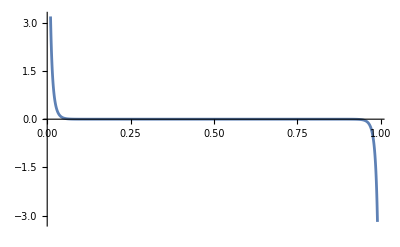

```mathematica
(Z Zb)^-Δϕ ϕϕϕϕ4pt-((1-Z) (1-Zb))^-Δϕ(ϕϕϕϕ4pt/.{Z->1-Z,Zb->1-Zb})/.Zb->0.5//Plot[#,{Z,0.01,0.99},ImageSize->400,PlotRange->All]&
```

```mathematica
(Z Zb)^-Δϕ ϕϕϕϕ4pt-((1-Z) (1-Zb))^-Δϕ(ϕϕϕϕ4pt/.{Z->1-Z,Zb->1-Zb})//Plot3D[#,{Z,0.1,0.9},{Zb,0.1,0.9},BoxRatios->{1,1,1},ImageSize->400,PlotRange->All]&
```

-Graphics3D-

```mathematica
(Z Zb)^-Δϕ ϕϕϕϕ4pt-((1-Z) (1-Zb))^-Δϕ(ϕϕϕϕ4pt/.{Z->1-Z,Zb->1-Zb})//Plot3D[#,{Z,0.2,0.8},{Zb,0.2,0.8},BoxRatios->{1,1,1},ImageSize->400,PlotRange->All]&
```

-Graphics3D-

```mathematica
(*Define the custom four-point function F(Z)*)ClearAll[Fmodel]
Fmodel[Z_]:=Module[{x1=Re[Z],x2=Im[Z]},((*Real part of F(Z)*)ReF=
0.0426069881903328*(-0.119187099059722*Sin[2.16447973251343*x1+8.20879936218262]+0.104612849033642*Sin[2.17511987686157*x2-1.81255984306335]-1)^2+0.0117165281617866*Exp[1.62476425972469*x1+0.387948007898936*x2]+0.0384921365387006*Sin[2.09151983261108*x1+7.82631969451904]+0.00467880887065934*Sin[5.61032009124756*x2+1.80879986286163]-0.00278585869818926*Sin[1.94508732247454*(0.142858738572167-x1)^2-0.214186366647482*Sin[6.02503967285156*x2+7.40719985961914]+3.61751382797956]+0.0690936297178268*Sin[0.124536964965273*Sin[3.68384003639221*x1-2.02495980262756]-0.12913981660563*Sin[2.96407985687256*x2+7.1832799911499]+6.87010421403227]-0.144930062966959;
(*Imaginary part of F(Z)*)ImF=0.00184248466325946*(-(0.142858738572167-x1)^2+0.110116581488483*Sin[6.02503967285156*x2+7.40719985961914]-0.766339588690362)^3+0.0499011229088968*(-0.048276858301737*Sin[2.16447973251343*x1+8.20879936218262]+0.0423735431869809*Sin[2.17511987686157*x2-1.81255984306335]-1)^2+0.00618865363230556*Sin[2.09151983261108*x1+7.82631969451904]+0.000752245266592492*Sin[5.61032009124756*x2+1.80879986286163]+0.0112671386450529*Sin[1.99123759216869*x1+0.475451532437211*x2-0.0459579730052378]+0.0256963595747948*Sin[0.237639982872395*Sin[3.68384003639221*x1-2.02495980262756]-0.246423090645123*Sin[2.96407985687256*x2+7.1832799911499]+0.848663631106234]-0.0761594627832133;
(*Extract real and imaginary parts*)ReF+I*ImF)]
```

```mathematica
ϕϕϕϕ4pt
```

1.76855+1.83275 (-1/2+Z)+1.98794 (-1/2+Z)^2+3.84769 (-1/2+Z)^3+6.26951 (-1/2+Z)^4+12.0288 (-1/2+Z)^5+21.2253 (-1/2+Z)^6+41.0076 (-1/2+Z)^7+74.9585 (-1/2+Z)^8+145.632 (-1/2+Z)^9+271.558 (-1/2+Z)^10+529.77 (-1/2+Z)^11+1000.56 (-1/2+Z)^12+1958.02 (-1/2+Z)^13+3731.05 (-1/2+Z)^14+7319.05 (-1/2+Z)^15+14038. (-1/2+Z)^16+27590.8 (-1/2+Z)^17+53184.6 (-1/2+Z)^18+104695. (-1/2+Z)^19+202611. (-1/2+Z)^20+399364. (-1/2+Z)^21+775342. (-1/2+Z)^22+1.52995×10^6 (-1/2+Z)^23+2.97816×10^6 (-1/2+Z)^24+5.88224×10^6 (-1/2+Z)^25+1.14756×10^7 (-1/2+Z)^26+2.26842×10^7 (-1/2+Z)^27+4.43377×10^7 (-1/2+Z)^28+8.77065×10^7 (-1/2+Z)^29+1.71706×10^8 (-1/2+Z)^30+3.39874×10^8 (-1/2+Z)^31+6.66326×10^8 (-1/2+Z)^32+1.31966×10^9 (-1/2+Z)^33+2.59041×10^9 (-1/2+Z)^34+5.13287×10^9 (-1/2+Z)^35+1.83275 (-1/2+Zb)+4.31404 (-1/2+Z) (-1/2+Zb)+4.56252 (-1/2+Z)^2 (-1/2+Zb)+8.59289 (-1/2+Z)^3 (-1/2+Zb)+13.7106 (-1/2+Z)^4 (-1/2+Zb)+26.2388 (-1/2+Z)^5 (-1/2+Zb)+45.7337 (-1/2+Z)^6 (-1/2+Zb)+88.4376 (-1/2+Z)^7 (-1/2+Zb)+160.283 (-1/2+Z)^8 (-1/2+Zb)+311.936 (-1/2+Z)^9 (-1/2+Zb)+577.905 (-1/2+Z)^10 (-1/2+Zb)+1129.54 (-1/2+Z)^11 (-1/2+Zb)+2122.26 (-1/2+Z)^12 (-1/2+Zb)+4160.92 (-1/2+Z)^13 (-1/2+Zb)+7894.45 (-1/2+Z)^14 (-1/2+Zb)+15514.1 (-1/2+Z)^15 (-1/2+Zb)+29646.2 (-1/2+Z)^16 (-1/2+Zb)+58367.1 (-1/2+Z)^17 (-1/2+Zb)+112147. (-1/2+Z)^18 (-1/2+Zb)+221118. (-1/2+Z)^19 (-1/2+Zb)+426694. (-1/2+Z)^20 (-1/2+Zb)+842328. (-1/2+Z)^21 (-1/2+Zb)+1.63113×10^6 (-1/2+Z)^22 (-1/2+Zb)+3.22325×10^6 (-1/2+Z)^23 (-1/2+Zb)+6.25969×10^6 (-1/2+Z)^24 (-1/2+Zb)+1.23803×10^7 (-1/2+Z)^25 (-1/2+Zb)+2.41013×10^7 (-1/2+Z)^26 (-1/2+Zb)+4.77027×10^7 (-1/2+Z)^27 (-1/2+Zb)+9.30557×10^7 (-1/2+Z)^28 (-1/2+Zb)+1.84301×10^8 (-1/2+Z)^29 (-1/2+Zb)+3.60159×10^8 (-1/2+Z)^30 (-1/2+Zb)+7.13716×10^8 (-1/2+Z)^31 (-1/2+Zb)+1.39689×10^9 (-1/2+Z)^32 (-1/2+Zb)+2.76956×10^9 (-1/2+Z)^33 (-1/2+Zb)+5.42791×10^9 (-1/2+Z)^34 (-1/2+Zb)+1.98794 (-1/2+Zb)^2+4.56252 (-1/2+Z) (-1/2+Zb)^2+4.97458 (-1/2+Z)^2 (-1/2+Zb)^2+9.2498 (-1/2+Z)^3 (-1/2+Zb)^2+14.5435 (-1/2+Z)^4 (-1/2+Zb)^2+27.9644 (-1/2+Z)^5 (-1/2+Zb)^2+48.1818 (-1/2+Z)^6 (-1/2+Zb)^2+93.731 (-1/2+Z)^7 (-1/2+Zb)^2+168.314 (-1/2+Z)^8 (-1/2+Zb)^2+329.445 (-1/2+Z)^9 (-1/2+Zb)^2+605.671 (-1/2+Z)^10 (-1/2+Zb)^2+1190.03 (-1/2+Z)^11 (-1/2+Zb)^2+2221.26 (-1/2+Z)^12 (-1/2+Zb)^2+4375.84 (-1/2+Z)^13 (-1/2+Zb)^2+8254.57 (-1/2+Z)^14 (-1/2+Zb)^2+16292.7 (-1/2+Z)^15 (-1/2+Zb)^2+30975. (-1/2+Z)^16 (-1/2+Zb)^2+61227.9 (-1/2+Z)^17 (-1/2+Zb)^2+117102. (-1/2+Z)^18 (-1/2+Zb)^2+231744. (-1/2+Z)^19 (-1/2+Zb)^2+445324. (-1/2+Z)^20 (-1/2+Zb)^2+882130. (-1/2+Z)^21 (-1/2+Zb)^2+1.70163×10^6 (-1/2+Z)^22 (-1/2+Zb)^2+3.37337×10^6 (-1/2+Z)^23 (-1/2+Zb)^2+6.52789×10^6 (-1/2+Z)^24 (-1/2+Zb)^2+1.29497×10^7 (-1/2+Z)^25 (-1/2+Zb)^2+2.5126×10^7 (-1/2+Z)^26 (-1/2+Zb)^2+4.98719×10^7 (-1/2+Z)^27 (-1/2+Zb)^2+9.69855×10^7 (-1/2+Z)^28 (-1/2+Zb)^2+1.92598×10^8 (-1/2+Z)^29 (-1/2+Zb)^2+3.75278×10^8 (-1/2+Z)^30 (-1/2+Zb)^2+7.45562×10^8 (-1/2+Z)^31 (-1/2+Zb)^2+1.45521×10^9 (-1/2+Z)^32 (-1/2+Zb)^2+2.89215×10^9 (-1/2+Z)^33 (-1/2+Zb)^2+3.84769 (-1/2+Zb)^3+8.59289 (-1/2+Z) (-1/2+Zb)^3+9.2498 (-1/2+Z)^2 (-1/2+Zb)^3+17.7014 (-1/2+Z)^3 (-1/2+Zb)^3+27.8225 (-1/2+Z)^4 (-1/2+Zb)^3+54.0157 (-1/2+Z)^5 (-1/2+Zb)^3+93.0099 (-1/2+Z)^6 (-1/2+Zb)^3+181.904 (-1/2+Z)^7 (-1/2+Zb)^3+326.435 (-1/2+Z)^8 (-1/2+Zb)^3+641.21 (-1/2+Z)^9 (-1/2+Zb)^3+1178.1 (-1/2+Z)^10 (-1/2+Zb)^3+2320.82 (-1/2+Z)^11 (-1/2+Zb)^3+4329.39 (-1/2+Z)^12 (-1/2+Zb)^3+8546.33 (-1/2+Z)^13 (-1/2+Zb)^3+16113. (-1/2+Z)^14 (-1/2+Zb)^3+31856.8 (-1/2+Z)^15 (-1/2+Zb)^3+60534.2 (-1/2+Z)^16 (-1/2+Zb)^3+119826. (-1/2+Z)^17 (-1/2+Zb)^3+229066. (-1/2+Z)^18 (-1/2+Zb)^3+453871. (-1/2+Z)^19 (-1/2+Zb)^3+871784. (-1/2+Z)^20 (-1/2+Zb)^3+1.72873×10^6 (-1/2+Z)^21 (-1/2+Zb)^3+3.33334×10^6 (-1/2+Z)^22 (-1/2+Zb)^3+6.61436×10^6 (-1/2+Z)^23 (-1/2+Zb)^3+1.27946×10^7 (-1/2+Z)^24 (-1/2+Zb)^3+2.54028×10^7 (-1/2+Z)^25 (-1/2+Zb)^3+4.92705×10^7 (-1/2+Z)^26 (-1/2+Zb)^3+9.78709×10^7 (-1/2+Z)^27 (-1/2+Zb)^3+1.90262×10^8 (-1/2+Z)^28 (-1/2+Zb)^3+3.78097×10^8 (-1/2+Z)^29 (-1/2+Zb)^3+7.36478×10^8 (-1/2+Z)^30 (-1/2+Zb)^3+1.46411×10^9 (-1/2+Z)^31 (-1/2+Zb)^3+2.85677×10^9 (-1/2+Z)^32 (-1/2+Zb)^3+6.26951 (-1/2+Zb)^4+13.7106 (-1/2+Z) (-1/2+Zb)^4+14.5435 (-1/2+Z)^2 (-1/2+Zb)^4+27.8225 (-1/2+Z)^3 (-1/2+Zb)^4+43.1903 (-1/2+Z)^4 (-1/2+Zb)^4+84.2213 (-1/2+Z)^5 (-1/2+Zb)^4+143.835 (-1/2+Z)^6 (-1/2+Zb)^4+282.476 (-1/2+Z)^7 (-1/2+Zb)^4+503.824 (-1/2+Z)^8 (-1/2+Zb)^4+993.26 (-1/2+Z)^9 (-1/2+Zb)^4+1816.05 (-1/2+Z)^10 (-1/2+Zb)^4+3588.97 (-1/2+Z)^11 (-1/2+Zb)^4+6667.94 (-1/2+Z)^12 (-1/2+Zb)^4+13199.9 (-1/2+Z)^13 (-1/2+Zb)^4+24800.4 (-1/2+Z)^14 (-1/2+Zb)^4+49156.8 (-1/2+Z)^15 (-1/2+Zb)^4+93123.8 (-1/2+Z)^16 (-1/2+Zb)^4+184759. (-1/2+Z)^17 (-1/2+Zb)^4+352242. (-1/2+Z)^18 (-1/2+Zb)^4+699393. (-1/2+Z)^19 (-1/2+Zb)^4+1.34011×10^6 (-1/2+Z)^20 (-1/2+Zb)^4+2.66253×10^6 (-1/2+Z)^21 (-1/2+Zb)^4+5.12253×10^6 (-1/2+Z)^22 (-1/2+Zb)^4+1.01828×10^7 (-1/2+Z)^23 (-1/2+Zb)^4+1.96573×10^7 (-1/2+Z)^24 (-1/2+Zb)^4+3.90929×10^7 (-1/2+Z)^25 (-1/2+Zb)^4+7.56811×10^7 (-1/2+Z)^26 (-1/2+Zb)^4+1.50566×10^8 (-1/2+Z)^27 (-1/2+Zb)^4+2.92193×10^8 (-1/2+Z)^28 (-1/2+Zb)^4+5.81505×10^8 (-1/2+Z)^29 (-1/2+Zb)^4+1.13084×10^9 (-1/2+Z)^30 (-1/2+Zb)^4+2.25119×10^9 (-1/2+Z)^31 (-1/2+Zb)^4+12.0288 (-1/2+Zb)^5+26.2388 (-1/2+Z) (-1/2+Zb)^5+27.9644 (-1/2+Z)^2 (-1/2+Zb)^5+54.0157 (-1/2+Z)^3 (-1/2+Zb)^5+84.2213 (-1/2+Z)^4 (-1/2+Zb)^5+164.548 (-1/2+Z)^5 (-1/2+Zb)^5+281.751 (-1/2+Z)^6 (-1/2+Zb)^5+553.634 (-1/2+Z)^7 (-1/2+Zb)^5+989.25 (-1/2+Z)^8 (-1/2+Zb)^5+1950.47 (-1/2+Z)^9 (-1/2+Zb)^5+3571.1 (-1/2+Z)^10 (-1/2+Zb)^5+7056.95 (-1/2+Z)^11 (-1/2+Zb)^5+13125.6 (-1/2+Z)^12 (-1/2+Zb)^5+25979.9 (-1/2+Z)^13 (-1/2+Zb)^5+48856.7 (-1/2+Z)^14 (-1/2+Zb)^5+96821. (-1/2+Z)^15 (-1/2+Zb)^5+183564. (-1/2+Z)^16 (-1/2+Zb)^5+364122. (-1/2+Z)^17 (-1/2+Zb)^5+694673. (-1/2+Z)^18 (-1/2+Zb)^5+1.37902×10^6 (-1/2+Z)^19 (-1/2+Zb)^5+2.64395×10^6 (-1/2+Z)^20 (-1/2+Zb)^5+5.25192×10^6 (-1/2+Z)^21 (-1/2+Zb)^5+1.01099×10^7 (-1/2+Z)^22 (-1/2+Zb)^5+2.00927×10^7 (-1/2+Z)^23 (-1/2+Zb)^5+3.8807×10^7 (-1/2+Z)^24 (-1/2+Zb)^5+7.7161×10^7 (-1/2+Z)^25 (-1/2+Zb)^5+1.49446×10^8 (-1/2+Z)^26 (-1/2+Zb)^5+2.97262×10^8 (-1/2+Z)^27 (-1/2+Zb)^5+5.77115×10^8 (-1/2+Z)^28 (-1/2+Zb)^5+1.14832×10^9 (-1/2+Z)^29 (-1/2+Zb)^5+2.23398×10^9 (-1/2+Z)^30 (-1/2+Zb)^5+21.2253 (-1/2+Zb)^6+45.7337 (-1/2+Z) (-1/2+Zb)^6+48.1818 (-1/2+Z)^2 (-1/2+Zb)^6+93.0099 (-1/2+Z)^3 (-1/2+Zb)^6+143.835 (-1/2+Z)^4 (-1/2+Zb)^6+281.751 (-1/2+Z)^5 (-1/2+Zb)^6+479.871 (-1/2+Z)^6 (-1/2+Zb)^6+945.308 (-1/2+Z)^7 (-1/2+Zb)^6+1682.47 (-1/2+Z)^8 (-1/2+Zb)^6+3324.64 (-1/2+Z)^9 (-1/2+Zb)^6+6068.09 (-1/2+Z)^10 (-1/2+Zb)^6+12014.8 (-1/2+Z)^11 (-1/2+Zb)^6+22289.3 (-1/2+Z)^12 (-1/2+Zb)^6+44194.2 (-1/2+Z)^13 (-1/2+Zb)^6+82926.6 (-1/2+Z)^14 (-1/2+Zb)^6+164594. (-1/2+Z)^15 (-1/2+Zb)^6+311456. (-1/2+Z)^16 (-1/2+Zb)^6+618681. (-1/2+Z)^17 (-1/2+Zb)^6+1.17831×10^6 (-1/2+Z)^18 (-1/2+Zb)^6+2.34211×10^6 (-1/2+Z)^19 (-1/2+Zb)^6+4.48356×10^6 (-1/2+Z)^20 (-1/2+Zb)^6+8.91664×10^6 (-1/2+Z)^21 (-1/2+Zb)^6+1.71405×10^7 (-1/2+Z)^22 (-1/2+Zb)^6+3.4103×10^7 (-1/2+Z)^23 (-1/2+Zb)^6+6.57823×10^7 (-1/2+Z)^24 (-1/2+Zb)^6+1.3093×10^8 (-1/2+Z)^25 (-1/2+Zb)^6+2.53288×10^8 (-1/2+Z)^26 (-1/2+Zb)^6+5.04295×10^8 (-1/2+Z)^27 (-1/2+Zb)^6+9.77985×10^8 (-1/2+Z)^28 (-1/2+Zb)^6+1.94771×10^9 (-1/2+Z)^29 (-1/2+Zb)^6+41.0076 (-1/2+Zb)^7+88.4376 (-1/2+Z) (-1/2+Zb)^7+93.731 (-1/2+Z)^2 (-1/2+Zb)^7+181.904 (-1/2+Z)^3 (-1/2+Zb)^7+282.476 (-1/2+Z)^4 (-1/2+Zb)^7+553.634 (-1/2+Z)^5 (-1/2+Zb)^7+945.308 (-1/2+Z)^6 (-1/2+Zb)^7+1861.86 (-1/2+Z)^7 (-1/2+Zb)^7+3319.67 (-1/2+Z)^8 (-1/2+Zb)^7+6557.5 (-1/2+Z)^9 (-1/2+Zb)^7+11985.1 (-1/2+Z)^10 (-1/2+Zb)^7+23720.8 (-1/2+Z)^11 (-1/2+Zb)^7+44054.9 (-1/2+Z)^12 (-1/2+Zb)^7+87314.7 (-1/2+Z)^13 (-1/2+Zb)^7+163992. (-1/2+Z)^14 (-1/2+Zb)^7+325366. (-1/2+Z)^15 (-1/2+Zb)^7+616177. (-1/2+Z)^16 (-1/2+Zb)^7+1.22353×10^6 (-1/2+Z)^17 (-1/2+Zb)^7+2.33191×10^6 (-1/2+Z)^18 (-1/2+Zb)^7+4.63347×10^6 (-1/2+Z)^19 (-1/2+Zb)^7+8.87558×10^6 (-1/2+Z)^20 (-1/2+Zb)^7+1.76453×10^7 (-1/2+Z)^21 (-1/2+Zb)^7+3.39389×10^7 (-1/2+Z)^22 (-1/2+Zb)^7+6.75038×10^7 (-1/2+Z)^23 (-1/2+Zb)^7+1.30278×10^8 (-1/2+Z)^24 (-1/2+Zb)^7+2.59221×10^8 (-1/2+Z)^25 (-1/2+Zb)^7+5.01707×10^8 (-1/2+Z)^26 (-1/2+Zb)^7+9.9861×10^8 (-1/2+Z)^27 (-1/2+Zb)^7+1.93746×10^9 (-1/2+Z)^28 (-1/2+Zb)^7+74.9585 (-1/2+Zb)^8+160.283 (-1/2+Z) (-1/2+Zb)^8+168.314 (-1/2+Z)^2 (-1/2+Zb)^8+326.435 (-1/2+Z)^3 (-1/2+Zb)^8+503.824 (-1/2+Z)^4 (-1/2+Zb)^8+989.25 (-1/2+Z)^5 (-1/2+Zb)^8+1682.47 (-1/2+Z)^6 (-1/2+Zb)^8+3319.67 (-1/2+Z)^7 (-1/2+Zb)^8+5901.84 (-1/2+Z)^8 (-1/2+Zb)^8+11676.6 (-1/2+Z)^9 (-1/2+Zb)^8+21292.5 (-1/2+Z)^10 (-1/2+Zb)^8+42200.8 (-1/2+Z)^11 (-1/2+Zb)^8+78228.5 (-1/2+Z)^12 (-1/2+Zb)^8+155238. (-1/2+Z)^13 (-1/2+Zb)^8+291093. (-1/2+Z)^14 (-1/2+Zb)^8+578184. (-1/2+Z)^15 (-1/2+Zb)^8+1.09343×10^6 (-1/2+Z)^16 (-1/2+Zb)^8+2.17338×10^6 (-1/2+Z)^17 (-1/2+Zb)^8+4.13708×10^6 (-1/2+Z)^18 (-1/2+Zb)^8+8.2279×10^6 (-1/2+Z)^19 (-1/2+Zb)^8+1.57432×10^7 (-1/2+Z)^20 (-1/2+Zb)^8+3.13253×10^7 (-1/2+Z)^21 (-1/2+Zb)^8+6.01899×10^7 (-1/2+Z)^22 (-1/2+Zb)^8+1.19811×10^8 (-1/2+Z)^23 (-1/2+Zb)^8+2.31012×10^8 (-1/2+Z)^24 (-1/2+Zb)^8+4.59994×10^8 (-1/2+Z)^25 (-1/2+Zb)^8+8.89532×10^8 (-1/2+Z)^26 (-1/2+Zb)^8+1.77176×10^9 (-1/2+Z)^27 (-1/2+Zb)^8+145.632 (-1/2+Zb)^9+311.936 (-1/2+Z) (-1/2+Zb)^9+329.445 (-1/2+Z)^2 (-1/2+Zb)^9+641.21 (-1/2+Z)^3 (-1/2+Zb)^9+993.26 (-1/2+Z)^4 (-1/2+Zb)^9+1950.47 (-1/2+Z)^5 (-1/2+Zb)^9+3324.64 (-1/2+Z)^6 (-1/2+Zb)^9+6557.5 (-1/2+Z)^7 (-1/2+Zb)^9+11676.6 (-1/2+Z)^8 (-1/2+Zb)^9+23091.5 (-1/2+Z)^9 (-1/2+Zb)^9+42159.3 (-1/2+Z)^10 (-1/2+Zb)^9+83519.9 (-1/2+Z)^11 (-1/2+Zb)^9+154977. (-1/2+Z)^12 (-1/2+Zb)^9+307404. (-1/2+Z)^13 (-1/2+Zb)^9+576913. (-1/2+Z)^14 (-1/2+Zb)^9+1.14542×10^6 (-1/2+Z)^15 (-1/2+Zb)^9+2.16773×10^6 (-1/2+Z)^16 (-1/2+Zb)^9+4.30709×10^6 (-1/2+Z)^17 (-1/2+Zb)^9+8.20387×10^6 (-1/2+Z)^18 (-1/2+Zb)^9+1.63102×10^7 (-1/2+Z)^19 (-1/2+Zb)^9+3.12256×10^7 (-1/2+Z)^20 (-1/2+Zb)^9+6.21106×10^7 (-1/2+Z)^21 (-1/2+Zb)^9+1.19404×10^8 (-1/2+Z)^22 (-1/2+Zb)^9+2.37603×10^8 (-1/2+Z)^23 (-1/2+Zb)^9+4.58347×10^8 (-1/2+Z)^24 (-1/2+Zb)^9+9.12395×10^8 (-1/2+Z)^25 (-1/2+Zb)^9+1.76514×10^9 (-1/2+Z)^26 (-1/2+Zb)^9+271.558 (-1/2+Zb)^10+577.905 (-1/2+Z) (-1/2+Zb)^10+605.671 (-1/2+Z)^2 (-1/2+Zb)^10+1178.1 (-1/2+Z)^3 (-1/2+Zb)^10+1816.05 (-1/2+Z)^4 (-1/2+Zb)^10+3571.1 (-1/2+Z)^5 (-1/2+Zb)^10+6068.09 (-1/2+Z)^6 (-1/2+Zb)^10+11985.1 (-1/2+Z)^7 (-1/2+Zb)^10+21292.5 (-1/2+Z)^8 (-1/2+Zb)^10+42159.3 (-1/2+Z)^9 (-1/2+Zb)^10+76834. (-1/2+Z)^10 (-1/2+Zb)^10+152377. (-1/2+Z)^11 (-1/2+Zb)^10+282325. (-1/2+Z)^12 (-1/2+Zb)^10+560545. (-1/2+Z)^13 (-1/2+Zb)^10+1.05066×10^6 (-1/2+Z)^14 (-1/2+Zb)^10+2.08782×10^6 (-1/2+Z)^15 (-1/2+Zb)^10+3.94686×10^6 (-1/2+Z)^16 (-1/2+Zb)^10+7.84823×10^6 (-1/2+Z)^17 (-1/2+Zb)^10+1.49342×10^7 (-1/2+Z)^18 (-1/2+Zb)^10+2.97122×10^7 (-1/2+Z)^19 (-1/2+Zb)^10+5.68336×10^7 (-1/2+Z)^20 (-1/2+Zb)^10+1.13122×10^8 (-1/2+Z)^21 (-1/2+Zb)^10+2.17297×10^8 (-1/2+Z)^22 (-1/2+Zb)^10+4.32667×10^8 (-1/2+Z)^23 (-1/2+Zb)^10+8.34026×10^8 (-1/2+Z)^24 (-1/2+Zb)^10+1.66118×10^9 (-1/2+Z)^25 (-1/2+Zb)^10+529.77 (-1/2+Zb)^11+1129.54 (-1/2+Z) (-1/2+Zb)^11+1190.03 (-1/2+Z)^2 (-1/2+Zb)^11+2320.82 (-1/2+Z)^3 (-1/2+Zb)^11+3588.97 (-1/2+Z)^4 (-1/2+Zb)^11+7056.95 (-1/2+Z)^5 (-1/2+Zb)^11+12014.8 (-1/2+Z)^6 (-1/2+Zb)^11+23720.8 (-1/2+Z)^7 (-1/2+Zb)^11+42200.8 (-1/2+Z)^8 (-1/2+Zb)^11+83519.9 (-1/2+Z)^9 (-1/2+Zb)^11+152377. (-1/2+Z)^10 (-1/2+Zb)^11+302060. (-1/2+Z)^11 (-1/2+Zb)^11+560153. (-1/2+Z)^12 (-1/2+Zb)^11+1.1117×10^6 (-1/2+Z)^13 (-1/2+Zb)^11+2.08526×10^6 (-1/2+Z)^14 (-1/2+Zb)^11+4.14213×10^6 (-1/2+Z)^15 (-1/2+Zb)^11+7.83542×10^6 (-1/2+Z)^16 (-1/2+Zb)^11+1.55749×10^7 (-1/2+Z)^17 (-1/2+Zb)^11+2.9654×10^7 (-1/2+Z)^18 (-1/2+Zb)^11+5.89778×10^7 (-1/2+Z)^19 (-1/2+Zb)^11+1.1287×10^8 (-1/2+Z)^20 (-1/2+Zb)^11+2.24587×10^8 (-1/2+Z)^21 (-1/2+Zb)^11+4.31608×10^8 (-1/2+Z)^22 (-1/2+Zb)^11+8.59139×10^8 (-1/2+Z)^23 (-1/2+Zb)^11+1.6568×10^9 (-1/2+Z)^24 (-1/2+Zb)^11+1000.56 (-1/2+Zb)^12+2122.26 (-1/2+Z) (-1/2+Zb)^12+2221.26 (-1/2+Z)^2 (-1/2+Zb)^12+4329.39 (-1/2+Z)^3 (-1/2+Zb)^12+6667.94 (-1/2+Z)^4 (-1/2+Zb)^12+13125.6 (-1/2+Z)^5 (-1/2+Zb)^12+22289.3 (-1/2+Z)^6 (-1/2+Zb)^12+44054.9 (-1/2+Z)^7 (-1/2+Zb)^12+78228.5 (-1/2+Z)^8 (-1/2+Zb)^12+154977. (-1/2+Z)^9 (-1/2+Zb)^12+282325. (-1/2+Z)^10 (-1/2+Zb)^12+560153. (-1/2+Z)^11 (-1/2+Zb)^12+1.0375×10^6 (-1/2+Z)^12 (-1/2+Zb)^12+2.06067×10^6 (-1/2+Z)^13 (-1/2+Zb)^12+3.86126×10^6 (-1/2+Z)^14 (-1/2+Zb)^12+7.67536×10^6 (-1/2+Z)^15 (-1/2+Zb)^12+1.45058×10^7 (-1/2+Z)^16 (-1/2+Zb)^12+2.88526×10^7 (-1/2+Z)^17 (-1/2+Zb)^12+5.48899×10^7 (-1/2+Z)^18 (-1/2+Zb)^12+1.09233×10^8 (-1/2+Z)^19 (-1/2+Zb)^12+2.08896×10^8 (-1/2+Z)^20 (-1/2+Zb)^12+4.15882×10^8 (-1/2+Z)^21 (-1/2+Zb)^12+7.98713×10^8 (-1/2+Z)^22 (-1/2+Zb)^12+1.59068×10^9 (-1/2+Z)^23 (-1/2+Zb)^12+1958.02 (-1/2+Zb)^13+4160.92 (-1/2+Z) (-1/2+Zb)^13+4375.84 (-1/2+Z)^2 (-1/2+Zb)^13+8546.33 (-1/2+Z)^3 (-1/2+Zb)^13+13199.9 (-1/2+Z)^4 (-1/2+Zb)^13+25979.9 (-1/2+Z)^5 (-1/2+Zb)^13+44194.2 (-1/2+Z)^6 (-1/2+Zb)^13+87314.7 (-1/2+Z)^7 (-1/2+Zb)^13+155238. (-1/2+Z)^8 (-1/2+Zb)^13+307404. (-1/2+Z)^9 (-1/2+Zb)^13+560545. (-1/2+Z)^10 (-1/2+Zb)^13+1.1117×10^6 (-1/2+Z)^11 (-1/2+Zb)^13+2.06067×10^6 (-1/2+Z)^12 (-1/2+Zb)^13+4.09131×10^6 (-1/2+Z)^13 (-1/2+Zb)^13+7.67132×10^6 (-1/2+Z)^14 (-1/2+Zb)^13+1.52435×10^7 (-1/2+Z)^15 (-1/2+Zb)^13+2.88256×10^7 (-1/2+Z)^16 (-1/2+Zb)^13+5.7316×10^7 (-1/2+Z)^17 (-1/2+Zb)^13+1.09094×10^8 (-1/2+Z)^18 (-1/2+Zb)^13+2.17035×10^8 (-1/2+Z)^19 (-1/2+Zb)^13+4.15243×10^8 (-1/2+Z)^20 (-1/2+Zb)^13+8.26454×10^8 (-1/2+Z)^21 (-1/2+Zb)^13+1.58787×10^9 (-1/2+Z)^22 (-1/2+Zb)^13+3731.05 (-1/2+Zb)^14+7894.45 (-1/2+Z) (-1/2+Zb)^14+8254.57 (-1/2+Z)^2 (-1/2+Zb)^14+16113. (-1/2+Z)^3 (-1/2+Zb)^14+24800.4 (-1/2+Z)^4 (-1/2+Zb)^14+48856.7 (-1/2+Z)^5 (-1/2+Zb)^14+82926.6 (-1/2+Z)^6 (-1/2+Zb)^14+163992. (-1/2+Z)^7 (-1/2+Zb)^14+291093. (-1/2+Z)^8 (-1/2+Zb)^14+576913. (-1/2+Z)^9 (-1/2+Zb)^14+1.05066×10^6 (-1/2+Z)^10 (-1/2+Zb)^14+2.08526×10^6 (-1/2+Z)^11 (-1/2+Zb)^14+3.86126×10^6 (-1/2+Z)^12 (-1/2+Zb)^14+7.67132×10^6 (-1/2+Z)^13 (-1/2+Zb)^14+1.43712×10^7 (-1/2+Z)^14 (-1/2+Zb)^14+2.85737×10^7 (-1/2+Z)^15 (-1/2+Zb)^14+5.39913×10^7 (-1/2+Z)^16 (-1/2+Zb)^14+1.07413×10^8 (-1/2+Z)^17 (-1/2+Zb)^14+2.04309×10^8 (-1/2+Z)^18 (-1/2+Zb)^14+4.06658×10^8 (-1/2+Z)^19 (-1/2+Zb)^14+7.77565×10^8 (-1/2+Z)^20 (-1/2+Zb)^14+1.54828×10^9 (-1/2+Z)^21 (-1/2+Zb)^14+7319.05 (-1/2+Zb)^15+15514.1 (-1/2+Z) (-1/2+Zb)^15+16292.7 (-1/2+Z)^2 (-1/2+Zb)^15+31856.8 (-1/2+Z)^3 (-1/2+Zb)^15+49156.8 (-1/2+Z)^4 (-1/2+Zb)^15+96821. (-1/2+Z)^5 (-1/2+Zb)^15+164594. (-1/2+Z)^6 (-1/2+Zb)^15+325366. (-1/2+Z)^7 (-1/2+Zb)^15+578184. (-1/2+Z)^8 (-1/2+Zb)^15+1.14542×10^6 (-1/2+Z)^9 (-1/2+Zb)^15+2.08782×10^6 (-1/2+Z)^10 (-1/2+Zb)^15+4.14213×10^6 (-1/2+Z)^11 (-1/2+Zb)^15+7.67536×10^6 (-1/2+Z)^12 (-1/2+Zb)^15+1.52435×10^7 (-1/2+Z)^13 (-1/2+Zb)^15+2.85737×10^7 (-1/2+Z)^14 (-1/2+Zb)^15+5.67933×10^7 (-1/2+Z)^15 (-1/2+Zb)^15+1.07369×10^8 (-1/2+Z)^16 (-1/2+Zb)^15+2.1354×10^8 (-1/2+Z)^17 (-1/2+Zb)^15+4.06356×10^8 (-1/2+Z)^18 (-1/2+Zb)^15+8.08586×10^8 (-1/2+Z)^19 (-1/2+Zb)^15+1.54671×10^9 (-1/2+Z)^20 (-1/2+Zb)^15+14038. (-1/2+Zb)^16+29646.2 (-1/2+Z) (-1/2+Zb)^16+30975. (-1/2+Z)^2 (-1/2+Zb)^16+60534.2 (-1/2+Z)^3 (-1/2+Zb)^16+93123.8 (-1/2+Z)^4 (-1/2+Zb)^16+183564. (-1/2+Z)^5 (-1/2+Zb)^16+311456. (-1/2+Z)^6 (-1/2+Zb)^16+616177. (-1/2+Z)^7 (-1/2+Zb)^16+1.09343×10^6 (-1/2+Z)^8 (-1/2+Zb)^16+2.16773×10^6 (-1/2+Z)^9 (-1/2+Zb)^16+3.94686×10^6 (-1/2+Z)^10 (-1/2+Zb)^16+7.83542×10^6 (-1/2+Z)^11 (-1/2+Zb)^16+1.45058×10^7 (-1/2+Z)^12 (-1/2+Zb)^16+2.88256×10^7 (-1/2+Z)^13 (-1/2+Zb)^16+5.39913×10^7 (-1/2+Z)^14 (-1/2+Zb)^16+1.07369×10^8 (-1/2+Z)^15 (-1/2+Zb)^16+2.02847×10^8 (-1/2+Z)^16 (-1/2+Zb)^16+4.0362×10^8 (-1/2+Z)^17 (-1/2+Zb)^16+7.67614×10^8 (-1/2+Z)^18 (-1/2+Zb)^16+1.52809×10^9 (-1/2+Z)^19 (-1/2+Zb)^16+27590.8 (-1/2+Zb)^17+58367.1 (-1/2+Z) (-1/2+Zb)^17+61227.9 (-1/2+Z)^2 (-1/2+Zb)^17+119826. (-1/2+Z)^3 (-1/2+Zb)^17+184759. (-1/2+Z)^4 (-1/2+Zb)^17+364122. (-1/2+Z)^5 (-1/2+Zb)^17+618681. (-1/2+Z)^6 (-1/2+Zb)^17+1.22353×10^6 (-1/2+Z)^7 (-1/2+Zb)^17+2.17338×10^6 (-1/2+Z)^8 (-1/2+Zb)^17+4.30709×10^6 (-1/2+Z)^9 (-1/2+Zb)^17+7.84823×10^6 (-1/2+Z)^10 (-1/2+Zb)^17+1.55749×10^7 (-1/2+Z)^11 (-1/2+Zb)^17+2.88526×10^7 (-1/2+Z)^12 (-1/2+Zb)^17+5.7316×10^7 (-1/2+Z)^13 (-1/2+Zb)^17+1.07413×10^8 (-1/2+Z)^14 (-1/2+Zb)^17+2.1354×10^8 (-1/2+Z)^15 (-1/2+Zb)^17+4.0362×10^8 (-1/2+Z)^16 (-1/2+Zb)^17+8.02889×10^8 (-1/2+Z)^17 (-1/2+Zb)^17+1.52758×10^9 (-1/2+Z)^18 (-1/2+Zb)^17+53184.6 (-1/2+Zb)^18+112147. (-1/2+Z) (-1/2+Zb)^18+117102. (-1/2+Z)^2 (-1/2+Zb)^18+229066. (-1/2+Z)^3 (-1/2+Zb)^18+352242. (-1/2+Z)^4 (-1/2+Zb)^18+694673. (-1/2+Z)^5 (-1/2+Zb)^18+1.17831×10^6 (-1/2+Z)^6 (-1/2+Zb)^18+2.33191×10^6 (-1/2+Z)^7 (-1/2+Zb)^18+4.13708×10^6 (-1/2+Z)^8 (-1/2+Zb)^18+8.20387×10^6 (-1/2+Z)^9 (-1/2+Zb)^18+1.49342×10^7 (-1/2+Z)^10 (-1/2+Zb)^18+2.9654×10^7 (-1/2+Z)^11 (-1/2+Zb)^18+5.48899×10^7 (-1/2+Z)^12 (-1/2+Zb)^18+1.09094×10^8 (-1/2+Z)^13 (-1/2+Zb)^18+2.04309×10^8 (-1/2+Z)^14 (-1/2+Zb)^18+4.06356×10^8 (-1/2+Z)^15 (-1/2+Zb)^18+7.67614×10^8 (-1/2+Z)^16 (-1/2+Zb)^18+1.52758×10^9 (-1/2+Z)^17 (-1/2+Zb)^18+104695. (-1/2+Zb)^19+221118. (-1/2+Z) (-1/2+Zb)^19+231744. (-1/2+Z)^2 (-1/2+Zb)^19+453871. (-1/2+Z)^3 (-1/2+Zb)^19+699393. (-1/2+Z)^4 (-1/2+Zb)^19+1.37902×10^6 (-1/2+Z)^5 (-1/2+Zb)^19+2.34211×10^6 (-1/2+Z)^6 (-1/2+Zb)^19+4.63347×10^6 (-1/2+Z)^7 (-1/2+Zb)^19+8.2279×10^6 (-1/2+Z)^8 (-1/2+Zb)^19+1.63102×10^7 (-1/2+Z)^9 (-1/2+Zb)^19+2.97122×10^7 (-1/2+Z)^10 (-1/2+Zb)^19+5.89778×10^7 (-1/2+Z)^11 (-1/2+Zb)^19+1.09233×10^8 (-1/2+Z)^12 (-1/2+Zb)^19+2.17035×10^8 (-1/2+Z)^13 (-1/2+Zb)^19+4.06658×10^8 (-1/2+Z)^14 (-1/2+Zb)^19+8.08586×10^8 (-1/2+Z)^15 (-1/2+Zb)^19+1.52809×10^9 (-1/2+Z)^16 (-1/2+Zb)^19+202611. (-1/2+Zb)^20+426694. (-1/2+Z) (-1/2+Zb)^20+445324. (-1/2+Z)^2 (-1/2+Zb)^20+871784. (-1/2+Z)^3 (-1/2+Zb)^20+1.34011×10^6 (-1/2+Z)^4 (-1/2+Zb)^20+2.64395×10^6 (-1/2+Z)^5 (-1/2+Zb)^20+4.48356×10^6 (-1/2+Z)^6 (-1/2+Zb)^20+8.87558×10^6 (-1/2+Z)^7 (-1/2+Zb)^20+1.57432×10^7 (-1/2+Z)^8 (-1/2+Zb)^20+3.12256×10^7 (-1/2+Z)^9 (-1/2+Zb)^20+5.68336×10^7 (-1/2+Z)^10 (-1/2+Zb)^20+1.1287×10^8 (-1/2+Z)^11 (-1/2+Zb)^20+2.08896×10^8 (-1/2+Z)^12 (-1/2+Zb)^20+4.15243×10^8 (-1/2+Z)^13 (-1/2+Zb)^20+7.77565×10^8 (-1/2+Z)^14 (-1/2+Zb)^20+1.54671×10^9 (-1/2+Z)^15 (-1/2+Zb)^20+399364. (-1/2+Zb)^21+842328. (-1/2+Z) (-1/2+Zb)^21+882130. (-1/2+Z)^2 (-1/2+Zb)^21+1.72873×10^6 (-1/2+Z)^3 (-1/2+Zb)^21+2.66253×10^6 (-1/2+Z)^4 (-1/2+Zb)^21+5.25192×10^6 (-1/2+Z)^5 (-1/2+Zb)^21+8.91664×10^6 (-1/2+Z)^6 (-1/2+Zb)^21+1.76453×10^7 (-1/2+Z)^7 (-1/2+Zb)^21+3.13253×10^7 (-1/2+Z)^8 (-1/2+Zb)^21+6.21106×10^7 (-1/2+Z)^9 (-1/2+Zb)^21+1.13122×10^8 (-1/2+Z)^10 (-1/2+Zb)^21+2.24587×10^8 (-1/2+Z)^11 (-1/2+Zb)^21+4.15882×10^8 (-1/2+Z)^12 (-1/2+Zb)^21+8.26454×10^8 (-1/2+Z)^13 (-1/2+Zb)^21+1.54828×10^9 (-1/2+Z)^14 (-1/2+Zb)^21+775342. (-1/2+Zb)^22+1.63113×10^6 (-1/2+Z) (-1/2+Zb)^22+1.70163×10^6 (-1/2+Z)^2 (-1/2+Zb)^22+3.33334×10^6 (-1/2+Z)^3 (-1/2+Zb)^22+5.12253×10^6 (-1/2+Z)^4 (-1/2+Zb)^22+1.01099×10^7 (-1/2+Z)^5 (-1/2+Zb)^22+1.71405×10^7 (-1/2+Z)^6 (-1/2+Zb)^22+3.39389×10^7 (-1/2+Z)^7 (-1/2+Zb)^22+6.01899×10^7 (-1/2+Z)^8 (-1/2+Zb)^22+1.19404×10^8 (-1/2+Z)^9 (-1/2+Zb)^22+2.17297×10^8 (-1/2+Z)^10 (-1/2+Zb)^22+4.31608×10^8 (-1/2+Z)^11 (-1/2+Zb)^22+7.98713×10^8 (-1/2+Z)^12 (-1/2+Zb)^22+1.58787×10^9 (-1/2+Z)^13 (-1/2+Zb)^22+1.52995×10^6 (-1/2+Zb)^23+3.22325×10^6 (-1/2+Z) (-1/2+Zb)^23+3.37337×10^6 (-1/2+Z)^2 (-1/2+Zb)^23+6.61436×10^6 (-1/2+Z)^3 (-1/2+Zb)^23+1.01828×10^7 (-1/2+Z)^4 (-1/2+Zb)^23+2.00927×10^7 (-1/2+Z)^5 (-1/2+Zb)^23+3.4103×10^7 (-1/2+Z)^6 (-1/2+Zb)^23+6.75038×10^7 (-1/2+Z)^7 (-1/2+Zb)^23+1.19811×10^8 (-1/2+Z)^8 (-1/2+Zb)^23+2.37603×10^8 (-1/2+Z)^9 (-1/2+Zb)^23+4.32667×10^8 (-1/2+Z)^10 (-1/2+Zb)^23+8.59139×10^8 (-1/2+Z)^11 (-1/2+Zb)^23+1.59068×10^9 (-1/2+Z)^12 (-1/2+Zb)^23+2.97816×10^6 (-1/2+Zb)^24+6.25969×10^6 (-1/2+Z) (-1/2+Zb)^24+6.52789×10^6 (-1/2+Z)^2 (-1/2+Zb)^24+1.27946×10^7 (-1/2+Z)^3 (-1/2+Zb)^24+1.96573×10^7 (-1/2+Z)^4 (-1/2+Zb)^24+3.8807×10^7 (-1/2+Z)^5 (-1/2+Zb)^24+6.57823×10^7 (-1/2+Z)^6 (-1/2+Zb)^24+1.30278×10^8 (-1/2+Z)^7 (-1/2+Zb)^24+2.31012×10^8 (-1/2+Z)^8 (-1/2+Zb)^24+4.58347×10^8 (-1/2+Z)^9 (-1/2+Zb)^24+8.34026×10^8 (-1/2+Z)^10 (-1/2+Zb)^24+1.6568×10^9 (-1/2+Z)^11 (-1/2+Zb)^24+5.88224×10^6 (-1/2+Zb)^25+1.23803×10^7 (-1/2+Z) (-1/2+Zb)^25+1.29497×10^7 (-1/2+Z)^2 (-1/2+Zb)^25+2.54028×10^7 (-1/2+Z)^3 (-1/2+Zb)^25+3.90929×10^7 (-1/2+Z)^4 (-1/2+Zb)^25+7.7161×10^7 (-1/2+Z)^5 (-1/2+Zb)^25+1.3093×10^8 (-1/2+Z)^6 (-1/2+Zb)^25+2.59221×10^8 (-1/2+Z)^7 (-1/2+Zb)^25+4.59994×10^8 (-1/2+Z)^8 (-1/2+Zb)^25+9.12395×10^8 (-1/2+Z)^9 (-1/2+Zb)^25+1.66118×10^9 (-1/2+Z)^10 (-1/2+Zb)^25+1.14756×10^7 (-1/2+Zb)^26+2.41013×10^7 (-1/2+Z) (-1/2+Zb)^26+2.5126×10^7 (-1/2+Z)^2 (-1/2+Zb)^26+4.92705×10^7 (-1/2+Z)^3 (-1/2+Zb)^26+7.56811×10^7 (-1/2+Z)^4 (-1/2+Zb)^26+1.49446×10^8 (-1/2+Z)^5 (-1/2+Zb)^26+2.53288×10^8 (-1/2+Z)^6 (-1/2+Zb)^26+5.01707×10^8 (-1/2+Z)^7 (-1/2+Zb)^26+8.89532×10^8 (-1/2+Z)^8 (-1/2+Zb)^26+1.76514×10^9 (-1/2+Z)^9 (-1/2+Zb)^26+2.26842×10^7 (-1/2+Zb)^27+4.77027×10^7 (-1/2+Z) (-1/2+Zb)^27+4.98719×10^7 (-1/2+Z)^2 (-1/2+Zb)^27+9.78709×10^7 (-1/2+Z)^3 (-1/2+Zb)^27+1.50566×10^8 (-1/2+Z)^4 (-1/2+Zb)^27+2.97262×10^8 (-1/2+Z)^5 (-1/2+Zb)^27+5.04295×10^8 (-1/2+Z)^6 (-1/2+Zb)^27+9.9861×10^8 (-1/2+Z)^7 (-1/2+Zb)^27+1.77176×10^9 (-1/2+Z)^8 (-1/2+Zb)^27+4.43377×10^7 (-1/2+Zb)^28+9.30557×10^7 (-1/2+Z) (-1/2+Zb)^28+9.69855×10^7 (-1/2+Z)^2 (-1/2+Zb)^28+1.90262×10^8 (-1/2+Z)^3 (-1/2+Zb)^28+2.92193×10^8 (-1/2+Z)^4 (-1/2+Zb)^28+5.77115×10^8 (-1/2+Z)^5 (-1/2+Zb)^28+9.77985×10^8 (-1/2+Z)^6 (-1/2+Zb)^28+1.93746×10^9 (-1/2+Z)^7 (-1/2+Zb)^28+8.77065×10^7 (-1/2+Zb)^29+1.84301×10^8 (-1/2+Z) (-1/2+Zb)^29+1.92598×10^8 (-1/2+Z)^2 (-1/2+Zb)^29+3.78097×10^8 (-1/2+Z)^3 (-1/2+Zb)^29+5.81505×10^8 (-1/2+Z)^4 (-1/2+Zb)^29+1.14832×10^9 (-1/2+Z)^5 (-1/2+Zb)^29+1.94771×10^9 (-1/2+Z)^6 (-1/2+Zb)^29+1.71706×10^8 (-1/2+Zb)^30+3.60159×10^8 (-1/2+Z) (-1/2+Zb)^30+3.75278×10^8 (-1/2+Z)^2 (-1/2+Zb)^30+7.36478×10^8 (-1/2+Z)^3 (-1/2+Zb)^30+1.13084×10^9 (-1/2+Z)^4 (-1/2+Zb)^30+2.23398×10^9 (-1/2+Z)^5 (-1/2+Zb)^30+3.39874×10^8 (-1/2+Zb)^31+7.13716×10^8 (-1/2+Z) (-1/2+Zb)^31+7.45562×10^8 (-1/2+Z)^2 (-1/2+Zb)^31+1.46411×10^9 (-1/2+Z)^3 (-1/2+Zb)^31+2.25119×10^9 (-1/2+Z)^4 (-1/2+Zb)^31+6.66326×10^8 (-1/2+Zb)^32+1.39689×10^9 (-1/2+Z) (-1/2+Zb)^32+1.45521×10^9 (-1/2+Z)^2 (-1/2+Zb)^32+2.85677×10^9 (-1/2+Z)^3 (-1/2+Zb)^32+1.31966×10^9 (-1/2+Zb)^33+2.76956×10^9 (-1/2+Z) (-1/2+Zb)^33+2.89215×10^9 (-1/2+Z)^2 (-1/2+Zb)^33+2.59041×10^9 (-1/2+Zb)^34+5.42791×10^9 (-1/2+Z) (-1/2+Zb)^34+5.13287×10^9 (-1/2+Zb)^35

```mathematica
Fmodel[Z]/.Z->1/2+I/2//Abs
```

0.0138362

```mathematica
(Z Zb)^-Δϕ ϕϕϕϕ4pt-((1-Z) (1-Zb))^-Δϕ(ϕϕϕϕ4pt/.{Z->1-Z,Zb->1-Zb}/.Zb->Conjugate[z]/.Z->z)//Plot3D[#,{Z,0.1,0.9},{Zb,0.1,0.9},BoxRatios->{1,1,1},ImageSize->400,PlotRange->All]&
```

```mathematica
(Z Zb)^-Δϕ Fmodel[Z]-((1-Z) (1-Zb))^-Δϕ(Fmodel[Z]/.{Z->1-Z,Zb->1-Zb})/.Zb->Conjugate[z]/.Z->z/.z->x1+I x2/.Δϕ->1/2//Evaluate
```

-1/(√((1-x1-ⅈ x2) (1-Conjugate[x1]+ⅈ Conjugate[x2])))(-0.14493+0.0117165 ⅇ^(1.62476 (1+Im[x2]-Re[x1])-0.387948 (Im[x1]+Re[x2]))+0.0384921 Sin[7.82632+2.09152 (1+Im[x2]-Re[x1])]+0.00467881 Sin[1.8088-5.61032 (Im[x1]+Re[x2])]+0.042607 (-1-0.119187 Sin[8.2088+2.16448 (1+Im[x2]-Re[x1])]-0.104613 Sin[1.81256+2.17512 (Im[x1]+Re[x2])])^2-0.00278586 Sin[3.61751+1.94509 (-0.857141-Im[x2]+Re[x1])^2-0.214186 Sin[7.4072-6.02504 (Im[x1]+Re[x2])]]+ⅈ (-0.0761595+0.00618865 Sin[7.82632+2.09152 (1+Im[x2]-Re[x1])]+0.00184248 (-0.76634-(-0.857141-Im[x2]+Re[x1])^2+0.110117 Sin[7.4072-6.02504 (Im[x1]+Re[x2])])^3+0.000752245 Sin[1.8088-5.61032 (Im[x1]+Re[x2])]-0.0112671 Sin[0.045958-1.99124 (1+Im[x2]-Re[x1])+0.475452 (Im[x1]+Re[x2])]+0.0499011 (-1-0.0482769 Sin[8.2088+2.16448 (1+Im[x2]-Re[x1])]-0.0423735 Sin[1.81256+2.17512 (Im[x1]+Re[x2])])^2+0.0256964 Sin[0.848664-0.23764 Sin[2.02496-3.68384 (1+Im[x2]-Re[x1])]-0.246423 Sin[7.18328-2.96408 (Im[x1]+Re[x2])]])+0.0690936 Sin[6.8701-0.124537 Sin[2.02496-3.68384 (1+Im[x2]-Re[x1])]-0.12914 Sin[7.18328-2.96408 (Im[x1]+Re[x2])]])+1/(√((x1+ⅈ x2) (Conjugate[x1]-ⅈ Conjugate[x2])))(-0.14493+0.0117165 ⅇ^(1.62476 (-Im[x2]+Re[x1])+0.387948 (Im[x1]+Re[x2]))+0.0384921 Sin[7.82632+2.09152 (-Im[x2]+Re[x1])]+0.042607 (-1-0.119187 Sin[8.2088+2.16448 (-Im[x2]+Re[x1])]-0.104613 Sin[1.81256-2.17512 (Im[x1]+Re[x2])])^2+0.00467881 Sin[1.8088+5.61032 (Im[x1]+Re[x2])]+ⅈ (-0.0761595+0.00618865 Sin[7.82632+2.09152 (-Im[x2]+Re[x1])]+0.0499011 (-1-0.0482769 Sin[8.2088+2.16448 (-Im[x2]+Re[x1])]-0.0423735 Sin[1.81256-2.17512 (Im[x1]+Re[x2])])^2-0.0112671 Sin[0.045958-1.99124 (-Im[x2]+Re[x1])-0.475452 (Im[x1]+Re[x2])]+0.000752245 Sin[1.8088+5.61032 (Im[x1]+Re[x2])]+0.00184248 (-0.76634-(0.142859+Im[x2]-Re[x1])^2+0.110117 Sin[7.4072+6.02504 (Im[x1]+Re[x2])])^3+0.0256964 Sin[0.848664-0.23764 Sin[2.02496-3.68384 (-Im[x2]+Re[x1])]-0.246423 Sin[7.18328+2.96408 (Im[x1]+Re[x2])]])+0.0690936 Sin[6.8701-0.124537 Sin[2.02496-3.68384 (-Im[x2]+Re[x1])]-0.12914 Sin[7.18328+2.96408 (Im[x1]+Re[x2])]]-0.00278586 Sin[3.61751+1.94509 (0.142859+Im[x2]-Re[x1])^2-0.214186 Sin[7.4072+6.02504 (Im[x1]+Re[x2])]])

```mathematica
(Z Zb)^-Δϕ ϕϕϕϕ4pt-((1-Z) (1-Zb))^-Δϕ(ϕϕϕϕ4pt/.{Z->1-Z,Zb->1-Zb})//Evaluate
```

```mathematica
ContourPlot[%993,{Z,0.1,0.9},{Zb,0.1,0.9},Contours->20,ContourShading->Automatic,ColorFunction->"Rainbow",PlotPoints->400]
```

-Graphics-

```mathematica
ContourPlot[Abs[Fmodel[x+I y]],{x,0,1},{y,0,1},Contours->20,ContourShading->Automatic,ColorFunction->"Rainbow"]
```

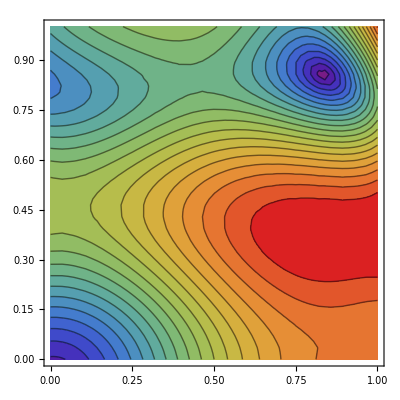

```mathematica
ContourPlot[Abs[Fmodel[x+I y]],{x,0,1},{y,0,1},Contours->20,ContourShading->Automatic,ColorFunction->"Rainbow"]
```

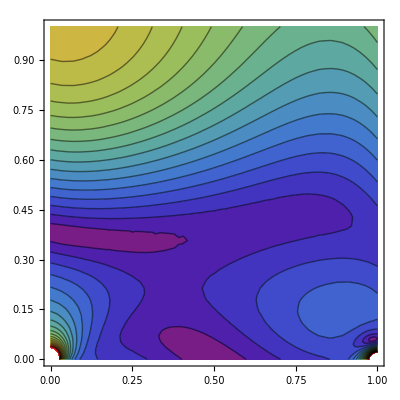

```mathematica
ContourPlot[Abs[(Z Zb)^-Δϕ Fmodel[Z]-((1-Z) (1-Zb))^-Δϕ(Fmodel[Z]/.{Z->1-Z,Zb->1-Zb})/.Zb->Conjugate[z]/.Z->z/.z->x+I y/.Δϕ->1/2],{x,0,1},{y,0,1},Contours->20,ContourShading->Automatic,ColorFunction->"Rainbow"]
```

```mathematica
ϕϕϕϕ4pt[Z,Z]/.Z->1/2//Evaluate
```

Null[1/2,1/2]

```mathematica
Abs[(Z Zb)^-Δϕ ϕϕϕϕ4pt-((1-Z) (1-Zb))^-Δϕ(ϕϕϕϕ4pt/.{Z->1-Z,Zb->1-Zb})]//Plot3D[#,{Z,0.1,0.9},{Zb,0.1,0.9},BoxRatios->{1,1,1},ImageSize->400,PlotRange->All]&
```

```mathematica
Abs[(Z Zb)^-Δϕ Fmodel[Z]-((1-Z) (1-Zb))^-Δϕ(Fmodel[Z]/.{Z->1-Z,Zb->1-Zb})/.Zb->Conjugate[z]/.Z->z/.z->x1+I x2/.Δϕ->1/2//Evaluate]//Plot3D[#,{x1,0.1,0.9},{x2,0.1,0.9},BoxRatios->{1,1,1},ImageSize->400,PlotRange->All]&
```

-Graphics3D-

```mathematica
{Z->1-Z,Zb->1-Zb}/.Z->z/.Zb->Conjugate[z]/.z->x1+I x2//ComplexExpand//Simplify
```

{x1+ⅈ x2→1-x1-ⅈ x2,x1-ⅈ x2→1-x1+ⅈ x2}

```mathematica
Solve[Z==x1+I x2&&Zb==x1-I x2,{x1,x2}]//Simplify
```

{{x1→(Z+Zb)/2,x2→-1/2 ⅈ (Z-Zb)}}

```mathematica
%916/.Zb->Conjugate[z]/.Z->z/.z->x1+I x2/.Δϕ->1/2/.x1->1/2/.x2->1/2
```

-0.00964798+0. ⅈ

```mathematica
Sin[Z]/.Z->1/2+I/2/.Δϕ->1/2//N
```

0.540613+0.457304 ⅈ

```mathematica
(Z Zb)^-Δϕ Fmodel[Z]-((1-Z) (1-Zb))^-Δϕ(Fmodel[Z]/.{Z->1-Z,Zb->1-Zb})/.Zb->Conjugate[Z]/.Z->1/2+I/2/.Δϕ->1/2//N
```

0.00590834-0.000890546 ⅈ